```mathematica
Integrate[(x+y)^2/(y-3^2),x,y]
```

1/6 x (3 (-9+y) (27+2 x+y)+2 (243+27 x+x^2) Log[-9+y])

```mathematica
h2[x_,y_]:=(x+y)^2/(1/100+(y-1/3)^2)
```

```mathematica
h2[u+v,u-v]
```

(4 u^2)/(1/100+(-1/3+u-v)^2)

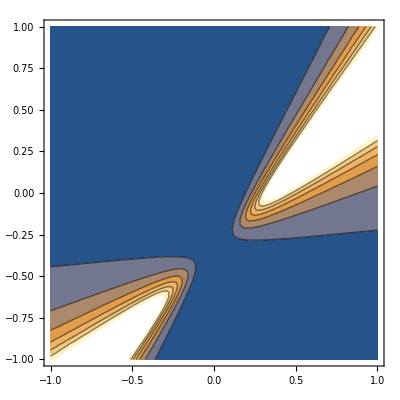

```mathematica
ContourPlot[h2[u+v,u-v],{u,-1,1},{v,-1,1}]
```

```mathematica
n = Integrate[ h2[u+v,u-v],{u,-1,1},{v,-1,1}]
```

1/4050(43200+14920 π-125840 ArcTan[3/70]-14920 ArcTan[3/50]+110920 ArcTan[3/10]+54000 ArcTan[50/3]+54000 ArcTan[70/3]+17946 Log[109]-3573 Log[2509]-14373 Log[4909])

```mathematica
n
```

1/4050(43200+14920 π-125840 ArcTan[3/70]-14920 ArcTan[3/50]+110920 ArcTan[3/10]+54000 ArcTan[50/3]+54000 ArcTan[70/3]+17946 Log[109]-3573 Log[2509]-14373 Log[4909])

```mathematica
1/n
```

4050/(43200+14920 π-125840 ArcTan[3/70]-14920 ArcTan[3/50]+110920 ArcTan[3/10]+54000 ArcTan[50/3]+54000 ArcTan[70/3]+17946 Log[109]-3573 Log[2509]-14373 Log[4909])

```mathematica
N[1/n, 25]
```

0.01890022674239546529975841

```mathematica
Integrate[h2[u+v,u-v]/n,{u,-1,1},{v, -1, 1}]
```

1